## Description

Receiver shape in spherical coordinates by using the most distant radial points

## Calculations: SphericalReceiverAngular

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
data=Import["C:\\Neo\\Programming\\SphericalReceiverAngular.csv"];
phiCoords=data[[1]];
thetaCoords=data[[2]]; 
rValues=data[[3;;-1]];
```

```mathematica
AppendTo[phiCoords,phiCoords[[1]]+2*Pi];
AppendTo[rValues,rValues[[1]]];
```

```mathematica
rFunc=ListInterpolation[
rValues,{
{phiCoords[[1]],phiCoords[[-1]]},
{thetaCoords[[1]],thetaCoords[[-1]]}
},InterpolationOrder->3
];
```

```mathematica
funcShape[phi_Real, theta_Real]:=Module[{r},
r=rFunc[phi,theta];
r*{
Cos[phi]*Sin[theta],
Sin[phi]*Sin[theta],
Cos[theta]
}
]
```

```mathematica
ParametricPlot3D[
funcShape[phi,theta],
{phi,phiCoords[[1]],phiCoords[[-1]]},
{theta,thetaCoords[[1]],thetaCoords[[-1]]},
PlotStyle->Opacity[1.],
AxesLabel->{"x","y","z"}
]
```

-Graphics3D-

### Export

```mathematica
table=Table[
r=rValues[[n,m]];
phi=phiCoords[[n]];
theta=thetaCoords[[m]];
r*{
Cos[phi]*Sin[theta],
Sin[phi]*Sin[theta],
Cos[theta]
},
{n,Length@phiCoords},
{m,Length@thetaCoords}
];
```

```mathematica
Export["radial.csv",Flatten[table,1]];
```

## Calculations: TubularReceiverAngular

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
data=Import["C:\\Neo\\Programming\\TubularReceiverAngular.csv"];
phiCoords=data[[1]]; 
hCoords=data[[2]]; 
rValues=data[[3;;-1]];
```

```mathematica
AppendTo[phiCoords,phiCoords[[1]]+2*Pi];
AppendTo[rValues,rValues[[1]]];
```

```mathematica
rFunc=ListInterpolation[
rValues,{
{phiCoords[[1]],phiCoords[[-1]]},
{hCoords[[1]],hCoords[[-1]]}
},InterpolationOrder->0
];
```

```mathematica
funcShape[phi_Real,h_Real]:=Module[{r,rMax=0.005},
r=rFunc[phi,h];
{
r*Cos[phi],
0.5+r*Sin[phi]
}
]
```

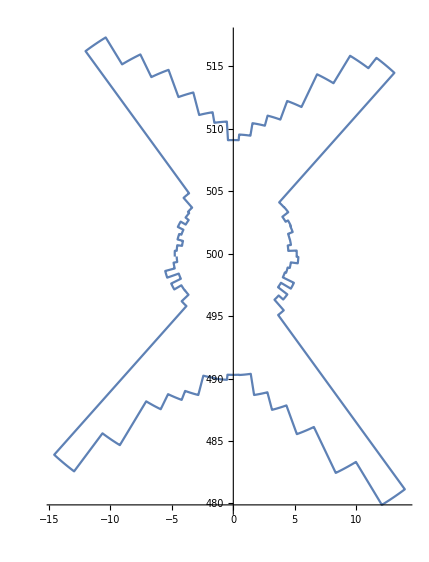

```mathematica
ParametricPlot[
1000.*funcShape[phi,0.],
{phi,phiCoords[[1]],phiCoords[[-1]]},
AspectRatio->Automatic,
PlotRange->All
]
```

### Export

```mathematica
mMiddle=Round[Length@hCoords/2];
table=Table[
r=rValues[[n,mMiddle]];
phi=phiCoords[[n]];
{
r*Cos[phi],
r*Sin[phi]
},
{n,Length@phiCoords}
];
```

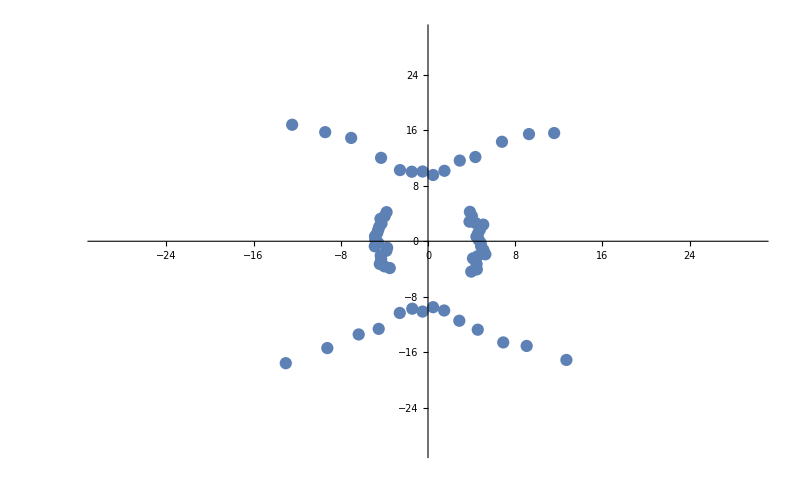

```mathematica
ListPlot[
1000*table,
AspectRatio->Automatic,
ImageSize->{800,500},
PlotRange->{{-30,30},{-30,30}}
]
```

```mathematica
(*Export["tubular.csv",Flatten[table,1]];*)
```